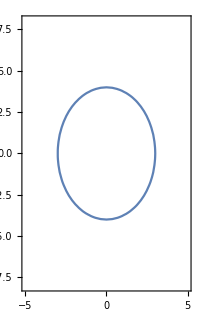

```mathematica
ContourPlot[x^2/9+y^2/16==1,{x,-5,5},{y,-8,8},AspectRatio->Automatic]
```

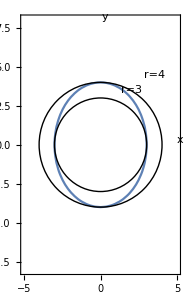

```mathematica
Show[ContourPlot[x^2/9+y^2/16==1,{x,-5,5},{y,-8,8},AspectRatio->Automatic],Graphics[{Circle[{0,0},4],Circle[{0,0},3]}],PlotRange->{{-5,5},{-8,8}},Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Black,Thick],TicksStyle->Directive[Black,Bold],Epilog->{Text["r=4",{3.5,4.5}],Text["r=3",{2,3.5}],Text["x",{5.2,0.3}],Text["y",{0.3,8.2}]}]
```

```mathematica
Integrate[2 t Exp[t],{t,0,1}]
```

2

```mathematica
f[x_,y_,z_]:=y ^-3;
c[t_]:={Log[t],t,2 };
a=1;
b=E;
pathIntegral=Integrate[f[c[t][[1]],c[t][[2]],c[t][[3]]]*Norm[D[c[t],t]],{t,a,b}]
Clear[f,c,a,b]
```

(2 √2 ⅇ^3-(1+ⅇ^2)^(3/2))/(3 ⅇ^3)

```mathematica
(*Three variables*)
```

```mathematica
f[x_,y_,z_]:=z;
c[t_]:={t*Cos[t],t*Sin[t],t}
a=0;
b=4;
AvePathValu=(Integrate[f[c[t][[1]],c[t][[2]],c[t][[3]]]*Norm[D[c[t],t]],{t,a,b}](*/Integrate[Norm[D[c[t],t]],{t,a,b}]*))
Clear[f,c,a,b];
```

(52 √2)/3

```mathematica
π/(4 √2)
```

```mathematica
(*double variables*)
```

```mathematica
f[x_,y_]:=y;
c[t_]:={Cos[t],Sin[t]}
a=0;
b=Pi;
AvePathValu=(Integrate[f[c[t][[1]],c[t][[2]]]*Norm[D[c[t],t]],{t,a,b}](*/Integrate[Norm[D[c[t],t]],{t,a,b}]*))
Clear[f,c,a,b]
```

2

```mathematica
Expand[(1+E^(-2))^3]
```

1+1/ⅇ^6+3/ⅇ^4+3/ⅇ^2

```mathematica
Expand[((1+E^(2))^3)/(E^6)]
```

1+1/ⅇ^6+3/ⅇ^4+3/ⅇ^2

```mathematica
ArcSinh[2]
```

ArcSinh[2]